### Notebook creates a map of the sky based on points randomly chosen on spherical shells which are slices of S^3 volume Number of superclusters is estimated to be in 1-10^6 range, with the typical distance between superclusters taken equal to the size of a typical void, Dv=10 Mps

```mathematica
(* calculate numerically the angular separation of supeclusters and voids 
treat superclusters as points at the vertices of 3D cubical voids *)
(* number of superclusters Nsc = 1 - 10^7 *)
(* number of voids Nv 
Nsc=(Nv+1)^3 
Nv=Nsc^(1/3) -1 
*)
(* volume V=Nv Dv^3 = 2 π^2 R^3
or
R ={Nv/(2 π^2)}^(1/3) Dv = (1/(2 π^2)^(1/3)(Nsc^(1/3)-1) Dv
*)
```

```mathematica
degRad=180/π
%//N
Print["Nsc is number of supeclusters"]
Nsc = 1 10^7
Nsc = 2 10^6
Dv=10

(* Nv is the number of voids, modeled as decsribed above *)
Nv=(Nsc^(1/3)-1)^3//N
Nv/2/π^2
Print["radius of 4D sphere in Mps"]
R=(Nv/(2 π^2))^(1/3) Dv
Print["V"]
V=2 π^2 R^3
Print["rho"]
rho=Nsc/V
L=π R
L/Dv
Nbin=Round[L/Dv]
delta=π/Nbin//N
Lbin=Nbin
corr=(1+Sqrt[2])/2
corr=1
Print["normalization checks: should be Nsc"]
Ncheck=Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho,{i,Lbin}]
Print["normalization checks: should be 1"]
Ncheck=Sum[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho,{i,Lbin}]/Nsc
Print["number of superclusters per 'layer' as function of ρ"]
(*
For[i=0,i<Nbin+1,i++,Print[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho]]
*)
slices=Table[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho,{i,0,Nbin}]
slices=Table[Round[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho],{i,0,Nbin}]
slices[[1]]
slices[[2]]
Total[slices]
```

180/π

57.2958

Nsc is number of supeclusters

10000000

2000000

10

1.95275×10^6

98927.7

radius of 4D sphere in Mps

462.494

V

1.95275×10^9

rho

0.00102419

1452.97

145.297

145

0.0216662

145

1/2 (1+√2)

1

normalization checks: should be Nsc

2.×10^6

normalization checks: should be 1

1.

number of superclusters per 'layer' as function of ρ

{0.,12.9476,51.7659,116.382,206.675,322.475,463.565,629.679,820.507,1035.69,1274.82,1537.46,1823.1,2131.22,2461.23,2812.51,3184.41,3576.22,3987.22,4416.63,4863.64,5327.41,5807.08,6301.74,6810.46,7332.3,7866.26,8411.35,8966.54,9530.8,10103.1,10682.2,11267.3,11857.,12450.4,13046.4,13643.7,14241.3,14838.1,15432.9,16024.6,16612.1,17194.4,17770.2,18338.6,18898.5,19448.7,19988.4,20516.4,21031.8,21533.6,22020.9,22492.7,22948.2,23386.5,23806.8,24208.3,24590.3,24952.,25292.7,25611.8,25908.8,26183.,26433.9,26661.1,26864.2,27042.7,27196.3,27324.8,27427.9,27505.4,27557.1,27583.,27583.,27557.1,27505.4,27427.9,27324.8,27196.3,27042.7,26864.2,26661.1,26433.9,26183.,25908.8,25611.8,25292.7,24952.,24590.3,24208.3,23806.8,23386.5,22948.2,22492.7,22020.9,21533.6,21031.8,20516.4,19988.4,19448.7,18898.5,18338.6,17770.2,17194.4,16612.1,16024.6,15432.9,14838.1,14241.3,13643.7,13046.4,12450.4,11857.,11267.3,10682.2,10103.1,9530.8,8966.54,8411.35,7866.26,7332.3,6810.46,6301.74,5807.08,5327.41,4863.64,4416.63,3987.22,3576.22,3184.41,2812.51,2461.23,2131.22,1823.1,1537.46,1274.82,1035.69,820.507,629.679,463.565,322.475,206.675,116.382,51.7659,12.9476,4.42736×10^-27}

{0,13,52,116,207,322,464,630,821,1036,1275,1537,1823,2131,2461,2813,3184,3576,3987,4417,4864,5327,5807,6302,6810,7332,7866,8411,8967,9531,10103,10682,11267,11857,12450,13046,13644,14241,14838,15433,16025,16612,17194,17770,18339,18898,19449,19988,20516,21032,21534,22021,22493,22948,23387,23807,24208,24590,24952,25293,25612,25909,26183,26434,26661,26864,27043,27196,27325,27428,27505,27557,27583,27583,27557,27505,27428,27325,27196,27043,26864,26661,26434,26183,25909,25612,25293,24952,24590,24208,23807,23387,22948,22493,22021,21534,21032,20516,19988,19449,18898,18339,17770,17194,16612,16025,15433,14838,14241,13644,13046,12450,11857,11267,10682,10103,9531,8967,8411,7866,7332,6810,6302,5807,5327,4864,4417,3987,3576,3184,2813,2461,2131,1823,1537,1275,1036,821,630,464,322,207,116,52,13,0}

0

13

1999998

```mathematica
Print["first layer:"]
slices[[2]]
Graphics3D[Point[SpherePoints[slices[[2]]]]]
testpoints2=SpherePoints[slices[[2]]];
Dimensions[testpoints2]

Print["second layer:"]
slices[[3]]
Graphics3D[Point[SpherePoints[slices[[3]]]]]
testpoints3=SpherePoints[slices[[3]]];
Dimensions[testpoints3]

Print["third layer:"]
slices[[4]]
Graphics3D[Point[SpherePoints[slices[[4]]]]]
testpoints4=SpherePoints[slices[[4]]];
Dimensions[testpoints4]

Print["fourth layer:"]
slices[[5]]
Graphics3D[Point[SpherePoints[slices[[5]]]]]
testpoints5=SpherePoints[slices[[5]]];
Dimensions[testpoints5]

Print["eleventh layer:"]
slices[[10]]
Graphics3D[Point[SpherePoints[slices[[10]]]]]
testpoints10=SpherePoints[slices[[10]]];
Dimensions[testpoints10]
```

first layer:

13

-Graphics3D-

{13,3}

second layer:

52

-Graphics3D-

{52,3}

third layer:

116

-Graphics3D-

{116,3}

fourth layer:

207

-Graphics3D-

{207,3}

eleventh layer:

1036

-Graphics3D-

{1036,3}

```mathematica
test=SpherePoints[slices[[2]]]
```

{{-0.442421,0.405294,-0.8},{0.0651633,-0.742502,-0.666667},{0.514682,0.671311,-0.533333},{-0.902505,-0.15964,-0.4},{0.813202,-0.517292,-0.266667},{-0.257286,0.957092,-0.133333},{-0.460907,-0.887448,0.},{0.930934,0.339976,0.133333},{-0.890874,0.36774,0.266667},{0.388461,-0.830119,0.4},{0.253166,0.807132,0.533333},{-0.64489,-0.373727,0.666667},{0.586005,-0.128832,0.8}}

```mathematica
Mbin=(Lbin+1)/2
Mbin=IntegerPart[%]//N
slices[[72]]
slices[[73]]
slices[[74]]
```

73

73.

27557

27583

27583

#### just to test the tools, modify the number of layers arbitrarily, the layers grow until (Lbin+1)/2, and the decrease symetrically after passing ρ=π/2, or the “equator”

```mathematica
Jbin=21
For[i=0,i<Jbin+1,i++,Print[Round[2 π R^3 (1-Cos[i delta]^2+Sin[i delta]^2)delta rho]]]
(* create images of celestial spheres obtained for subsequents lices of S^3
*)
sky=Table[SpherePoints[slices[[i]]],{i,2,Jbin}];
(*
sky//TableForm;
*)
(* create a sky map by combining images of celestial spheres obtained for subsequents lices of 
*)
(*technically : one needs to Flatten "sky" and rearrange to obtain a single array of (x,y,z} coordinates of all points (superclusters)
*)
sky=Flatten[sky];
len=Dimensions[sky]
len=Length[sky]
skymap=ArrayReshape[sky,{len/3,3}];
Dimensions[skymap]
(*
skymap//MatrixForm;
skymap//TableForm;
*)
Graphics3D[Point[skymap]]
```

21

0

13

52

116

207

322

464

630

821

1036

1275

1537

1823

2131

2461

2813

3184

3576

3987

4417

4864

5327

{107187}

107187

{35729,3}

-Graphics3D-

```mathematica
spherical=ToSphericalCoordinates[skymap];
```

```mathematica
Points=SpherePoints[100];
Point=DelaunayMesh[Points]
```

-Graphics3D-

```mathematica
(* solid angle - θ: angle formed by a ray r going around a chose direction, or apex angle 2θ

Ω = 2 π (1 - Cos[θ])

*)
```

180/π

ArcCos[1-2/n]

π/3

60.

ArcCos[4/5]

36.8699

ArcCos[49/50]

11.4783

ArcCos[99/100]

8.10961

ArcCos[499/500]

3.62431

ArcCos[4999/5000]

1.14593

ArcCos[9999/10000]

0.810291

ArcCos[24999/25000]

0.512471

ArcCos[49999/50000]

0.362371

ArcCos[99999/100000]

0.256235

apex angle in degrees for voids in slices of S^3 as defined in array slices[]

13

32.2042

52

15.9424

116

10.6549

207

7.97109

322

6.38925

464

5.32169

630

4.56665

821

4.00009

1036

3.56076

1275

3.20963

1537

2.92323

1823

2.6841

2131

2.48253

2461

2.31008

2813

2.1607

3184

2.0309

3576

1.91635

3987

1.81488

4417

1.72427

4864

1.64313

5327

1.57009

5807

1.5038

6302

1.44353

6810

1.38864

7332

1.33829

7866

1.29207

8411

1.2495

8967

1.21014

9531

1.17379

10103

1.14008

10682

1.10875

11267

1.07958

11857

1.05238

12450

1.02701

13046

1.00327

13644

0.981041

14241

0.960257

14838

0.94074

15433

0.922427

16025

0.905228

16612

0.889091

17194

0.873913

17770

0.859633

18339

0.846192

18898

0.833582

19449

0.821689

19988

0.810535

20516

0.800037

21032

0.790161

21534

0.780897

22021

0.772214

22493

0.764068

22948

0.756455

23387

0.749322

23807

0.742683

24208

0.736506

24590

0.730763

24952

0.725442

25293

0.720535

25612

0.716034

25909

0.711918

26183

0.708183

26434

0.704813

26661

0.701806

26864

0.699149

27043

0.696832

27196

0.694869

27325

0.693227

27428

0.691924

27505

0.690954

27557

0.690302

27583

0.689977

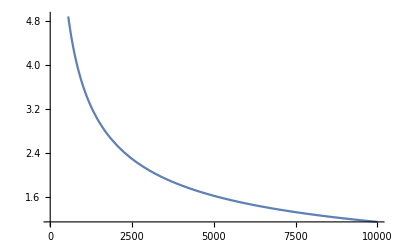

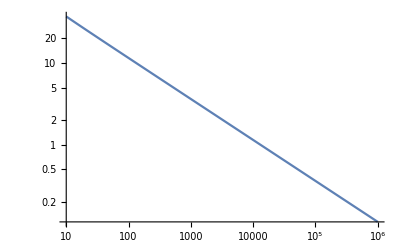

```mathematica
degRad=180/π
Thet[n_]=ArcCos[(1-2/n)]
Thet[4]
% degRad//N
Thet[10]
% degRad//N
Thet[100]
% degRad//N
Thet[200]
%degRad //N
Thet[1000]
%degRad //N
Thet[10000]
%degRad //N
Thet[20000]
% degRad//N
Thet[50000]
%degRad //N
Thet[100000]
%degRad //N
Thet[200000]
%degRad //N

Print["apex angle in degrees for voids in slices of S^3 as defined in array slices[]"]
For[i=2,i<Mbin+1,i++,j=slices[[i]];Print[j];Print[degRad N[Thet[j]]]]
Plot[N[degRad Thet[n]],{n,10,10000}]
LogLogPlot[ N[degRad Thet[n]],{n,10,1000000}]
```